```mathematica
(*WHITE DWARF  SINGLE SELF*)
```

```mathematica
R=7*10^6;(*in m*)
```

```mathematica
vesc=6 10^3*10^3;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^11;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;

b[mx_,sigmadmdm_]:=(ρx/mx*(6/π)^0.5*sigmadmdm*vbar*(vesc^2/vbar^2));
```

```mathematica
ldm[mx_,sigmadmdm_,T_,anncross_]:=mx*(b[mx,sigmadmdm]*b[mx,sigmadmdm]/(anncross/vth[mx,T]));
```

```mathematica
myticks={{Automatic,None},{{{-2,"10^-2"},{0,"1"},{2,"10^2"},{4,"10^4"},{6,"10^6"},{8,"10^8"}},None}};
```

```mathematica
(*ListLogPlot[{Table[{x,ldm[10^x,10^x/(5.62*10^27),10^7,3*10^-38]},{x,-1,8,0.1}]},Joined-> True,PlotStyle->{{Thick,Blue},{Thick,Red},{Thick,Green}},Frame->True,FrameStyle->Directive[14, "Times",Black],AxesOrigin->{-1,Automatic},FrameTicks->myticks,PlotLegends->Placed[{"<σ_av>=3*10^-38 m^3/s"},{0.8,0.9}],Epilog->Style[Text["σ_xx/m_x= 1 cm^2/g",Log@{3.0,0.5*10^32}],15],FrameLabel->{Style[" M_DM [GeV]",FontSize->20,Bold,FontFamily->"Times New Roman"],Style["L_DM\ =M_DM \ C_Tot [GeV S^-1]",FontSize->20,Bold,FontFamily->"Times New Roman"]},AspectRatio->1,ImageSize->450]*)
```

```mathematica
(*WHITE DWARF MULTI SELF*)
```

```mathematica
Tsun=10^17;
```

```mathematica
R=7*10^6;(*in m*)
```

```mathematica
vesc=6 10^3*10^3;(*in m/sec*)
vbar=20*10^3;(*in m/sec*)
```

```mathematica
ρx=10^6*10^3;(*in GeV/m^3*)(*Due to Overdensity*)
```

```mathematica
G=6.67*10^-11;(*in SI*)
ρ=10^11;(*in kg/m^3*)
```

```mathematica
kb=1.38*10^-23;(*in J/k*)
```

```mathematica
rth[mx_,T_]:=((9*kb*T)/(4*π*G*ρ*mx*1.78*10^-27))^0.5;
```

```mathematica
vth[mx_,T_]:=4/3*π*rth[mx,T]^3;
ϵ=10^-5;
umin[N_]:=vesc*(Log[1/ϵ]^(N-1)-1)^0.5;
umax=∞;
```

```mathematica
Nt=4/3 π R^3 10^36;
```

```mathematica
gN[u_,N_]:=vesc^2/(u^2+vesc^2)*Log[1/ϵ]^(N-1);
```

```mathematica
sigmaSat[Nchi_]:=(π *R^2)/Nchi;
```

```mathematica
tau[sigmadmdm_,Nchi_]:=Min[(3*sigmadmdm)/(2*sigmaSat[Nchi]),3/2];
```

```mathematica
pn[N_,sigmadmdm_,Nchi_]:=2/(Factorial[N]*tau[sigmadmdm,Nchi]*tau[sigmadmdm,Nchi])*(Gamma[N+2]-Gamma[(N+2),tau[sigmadmdm,Nchi]]);
```

```mathematica
fMB[u_,mx_]:=(3/(2*vbar^2))^(3/2)*4/(√π)*u^2*Exp[-3/(2*vbar^2)*u^2];
```

```mathematica
Cself[N_,mx_,sigmadmdm_,Nchi_]:= π R^2 pn[N,sigmadmdm,Nchi] ρx/mx NIntegrate[gN[u,N]*fMB[u,mx]/u*(u^2+vesc^2),{u,umin[N],umax},AccuracyGoal->5];
```

```mathematica
Integrate[x Exp[-3/2 x^2],{x,b2,Infinity}]
```

1/3 ⅇ^(-(3 b2^2)/2)

```mathematica
b1[N_?NumericQ,vesc_]:=vesc/vbar((Log[1/ϵ])^(N-1)-1)^(1/2)
```

```mathematica
b1[2.]
```

b1(2.)

```mathematica
(*Approximating the Error Function*)
a1=0.278393;
a2=0.230389;
a3=0.000972;
a4=0.078108;
```

```mathematica
erfcApprox[x_]:=1/(1+a1 x+a2 x^2+a3 x^3+a4 x^4)
```

```mathematica
Cself2[N_,mx_,sigmadmdm_,Nchi_,vesc_]:=(√(6π) R^2 pn[N,sigmadmdm,Nchi] ρx/mx vesc^2/vbar(Log[1/ϵ])^(N-1))Exp[-3/2 b1[N,vesc]^2]
```

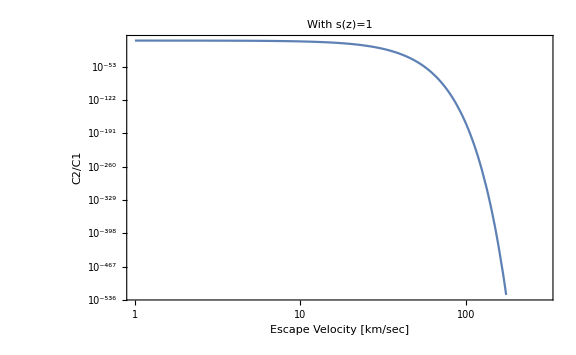

```mathematica
LogLogPlot[Cself2[2,10.,10^-28,10^45,x 10^3]/Cself2[1,10.,10^-28,10^45,x 10^3],{x,1,300},ImageSize->Large,Frame->True,FrameLabel->{"Escape Velocity [km/sec]","C2/C1"},PlotLabel->"With s(z)=1"]
```

```mathematica
Cselftot[mx_,sigmadmdm_,Nchi_,nDummy_?NumericQ,vesc_]:=Sum[Cself2[N,mx,sigmadmdm,Nchi,vesc],{N,1,nDummy}]
```

```mathematica
Cself2[6.,10,10^-28,10^45,10^4]
```

9.28594234485968×10^-32914

```mathematica
CA[sigmaAnn_,mx_,T_]:=sigmaAnn/vth[mx,T]
```

```mathematica
uM[N_?NumericQ,z0_,vesc_]:=vesc(1/(1-z0)^N-1)^(1/2)
```

```mathematica
CNdd[N_,mx_,sigmadmdm_,Nchi_,vesc_,z0_]:=√(6π) R^2 pn[N,sigmadmdm,Nchi] ρx/mx vbar/3(3(vesc/vbar)^2+2-(3(vesc/vbar)^2+2+3(uM[N,z0,vesc]/vbar)^2)Exp[-3/2(uM[N,z0,vesc]/vbar)^2])
```

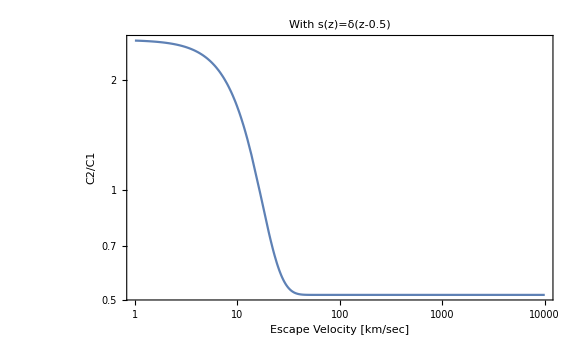

```mathematica
LogLogPlot[CNdd[2,10.,10^-28,10^45,x 10^3,0.5]/CNdd[1,10.,10^-28,10^45,x 10^3,0.5],{x,1,10^4},ImageSize->Large,Frame->True,FrameLabel->{"Escape Velocity [km/sec]","C2/C1"},PlotLabel->"With s(z)=δ(z-0.5)"]
```

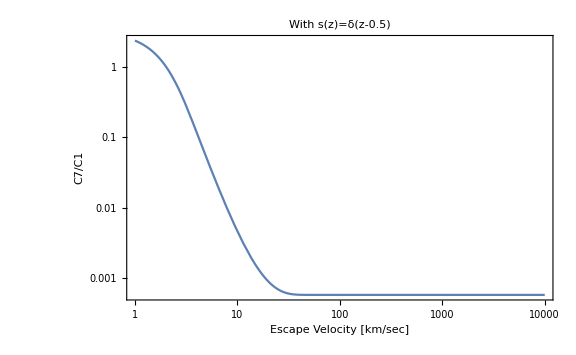

```mathematica
LogLogPlot[CNdd[7,10.,10^-28,10^45,x 10^3,0.5]/CNdd[1,10.,10^-28,10^45,x 10^3,0.5],{x,1,10^4},ImageSize->Large,Frame->True,FrameLabel->{"Escape Velocity [km/sec]","C7/C1"},PlotLabel->"With s(z)=δ(z-0.5)"]
```

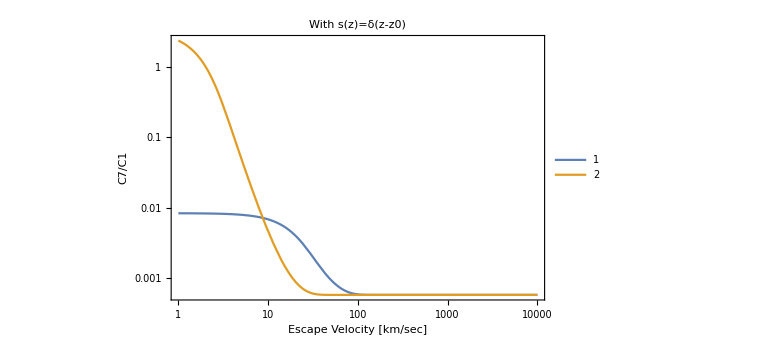

```mathematica
LogLogPlot[{CNdd[7,10.,10^-28,10^45,x 10^3,0.1]/CNdd[1,10.,10^-28,10^45,x 10^3,0.1],CNdd[7,10.,10^-28,10^45,x 10^3,0.5]/CNdd[1,10.,10^-28,10^45,x 10^3,0.5]},{x,1,10^4},ImageSize->Large,Frame->True,FrameLabel->{"Escape Velocity [km/sec]","C7/C1"},PlotLabel->"With s(z)=δ(z-z0)",PlotLegends->Automatic]
```

```mathematica
(*Nreq Plots*)
```

```mathematica
NminDelta[ve_,u_,η_]:=Log[ve^2/(ve^2+u^2)]/Log[1-η]
```

```mathematica
NmaxConst[ve_,u_,eps_]:=1/Log[Log[1/eps]] Log[u^2/ve^2(u^2+ve^2)+1]+1
```

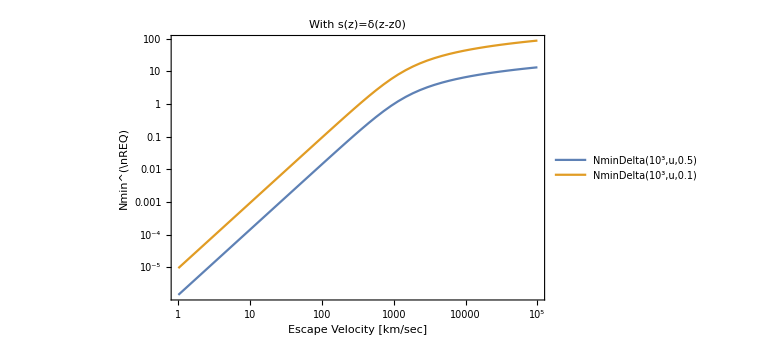

```mathematica
LogLogPlot[{NminDelta[10^3,u,0.5],NminDelta[10^3,u,0.1]},{u,1,10^5},ImageSize->Large,Frame->True,FrameLabel->{"Escape Velocity [km/sec]","Nmin^(\nREQ)"},PlotLabel->"With s(z)=δ(z-z0)",PlotLegends->"Expressions"]
```

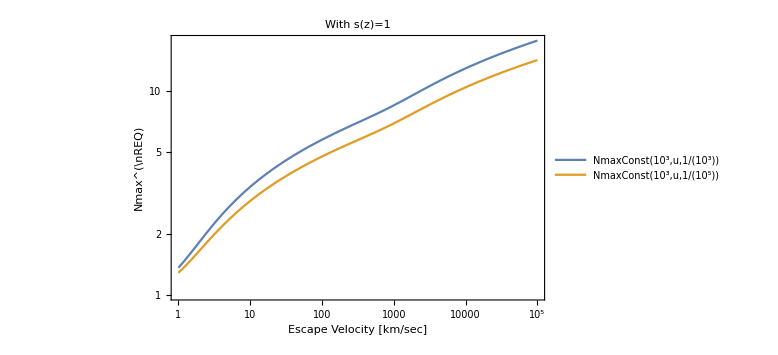

```mathematica
LogLogPlot[{NmaxConst[10^3,u,10^-3],NmaxConst[10^3,u,10^-5]},{u,1,10^5},ImageSize->Large,Frame->True,FrameLabel->{"Escape Velocity [km/sec]","Nmax^(\nREQ)"},PlotLabel->"With s(z)=1",PlotLegends->"Expressions"]
```